```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/home/zack/Desktop/snakingoscillators

#### Single trajectory runs

-Graphics- | -Graphics- | -Graphics-

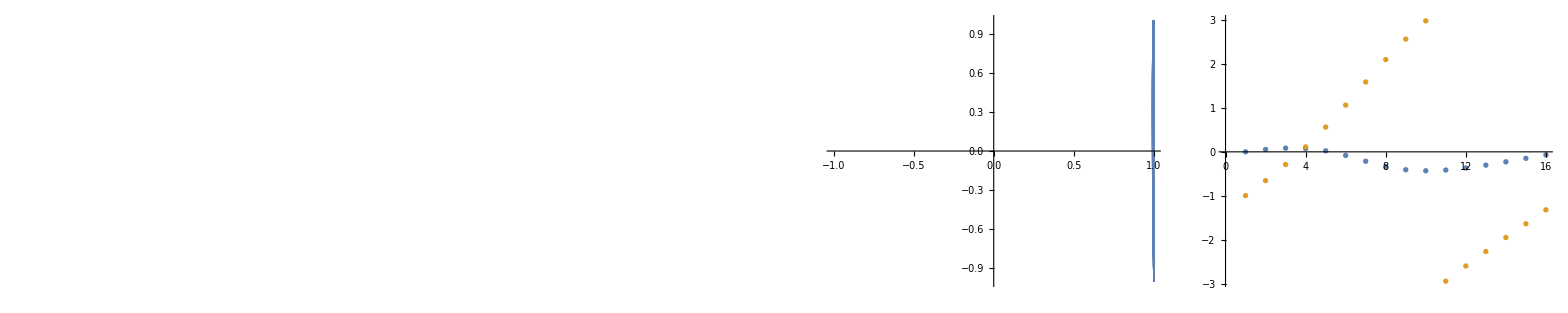

{72,0.245929,6.32951}

```mathematica
filebase="data/limit";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
Grid[{{rasterizeBackground[ListDensityPlot[theta[[-1000;;-1]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[-1000;;-1]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[orders,ImageSize->300]]}}]

phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
norms=Norm[Mod[#-dphases[[-1]]+Pi,2*Pi]-Pi]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
If[Length[periods]>0,
period=Round[Mean[periods]];
Grid[{{rasterizeBackground[ListDensityPlot[dphases[[1;;period,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;period,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[Length[periods]>0,{period,Mean[orders[[-period;;-1]]],Norm[Differences[dphases[[-period+1;;-1]]],2]}]
```

```mathematica
rasterizeBackground[ListDensityPlot[Mod[theta[[-100;;-1]]-phi[[-100;;-1]]+Pi,2*Pi]-Pi,AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]]
```

-Graphics-

```mathematica
rasterizeBackground[ListDensityPlot[theta[[-1000;;-1]]-phi[-1000;;-1]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]
```

$Aborted

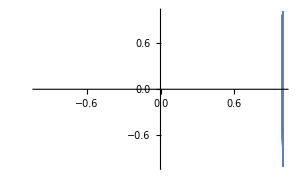

```mathematica
ListPlot[Transpose[{Cos[dphases[[-10000;;-1,2]]],Cos[dphases[[-10000;;-1,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]
```

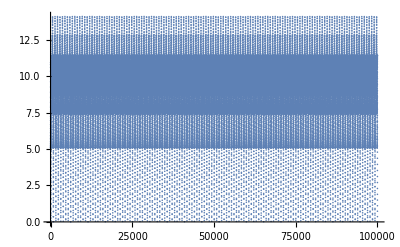

756.718

0.451916

```mathematica
ListPlot[norms]
N[Mean[periods]]
N[StandardDeviation[periods]]
```

```mathematica
-2*Round[period/0.1]
```

-30160

```mathematica
5000/(0.1*period)
```

33.1565

```mathematica
Length[dphases]
```

50000

```mathematica
Norm[Mod[dphases[[-Round[period];;-1]]-dphases[[-10*Round[period];;-9*Round[period]-1]]+Pi,2*Pi]-Pi]
```

35.9069

#### Chimeras from random initial conditions

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
dorder=0.01;
dperiod=0.01;
dnorm=0.01;
{bins,array}=HistogramList[vals[[All,2;;4]],{{dorder*(Range[1/dorder]-1)},{0.1+dperiod*(Range[3/dperiod]-1)},{dnorm*(Range[2/dnorm]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
SortBy[{#[[1]],#[[2]],#[[3]]*300,#[[4]]}&/@uniq,{#[[2]],#[[3]],#[[4]]}&]

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
Last/@ArrayRules[array][[1;;-2]]
```

30

{{93,0.151249,148.392,0.428905},{217,0.265035,148.392,0.748907},{701,0.304285,139.85,0.148142},{401,0.355924,250.071,1.44555},{18,0.416186,213.157,1.06305},{180,0.417352,148.477,1.20488},{596,0.423199,150.329,1.06356},{793,0.429596,218.024,1.3489},{682,0.429627,200.231,1.34339},{83,0.43118,148.645,1.33082},{907,0.433712,149.777,0.621012},{247,0.462647,148.408,0.333162},{612,0.467333,150.845,0.851777},{365,0.468335,148.482,0.891208},{785,0.470832,149.775,0.333178},{387,0.492707,148.392,0.160456},{854,0.506518,150.835,0.579826},{70,0.507703,148.495,0.586608},{658,0.509228,139.85,0.147551},{787,0.516819,148.645,1.01386},{683,0.5332,150.578,0.315608},{75,0.534699,148.406,0.317019},{39,0.546717,141.781,0.213861},{843,0.54815,140.619,0.215164},{725,0.59355,150.326,0.422165},{158,0.602228,148.65,0.69252},{117,0.67878,150.326,0.102679},{220,0.680311,150.326,0.10333},{898,0.68751,148.697,0.37302},{248,0.773605,150.326,0.0512991}}

{1,4,1,1,2,1,1,1,1,1,12,1,10,2,1,2,1,17,8,16,34,8,14,11,2,42,2,89,4,254}

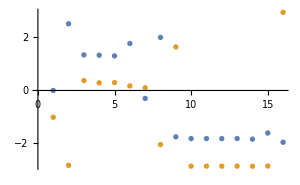
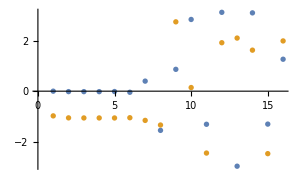
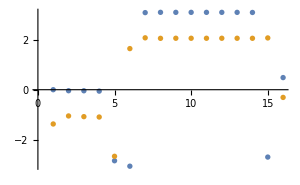
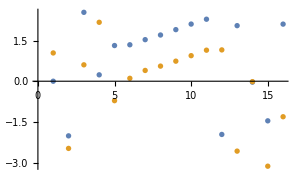
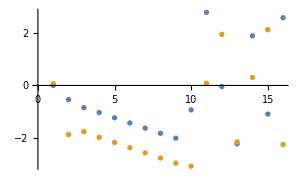
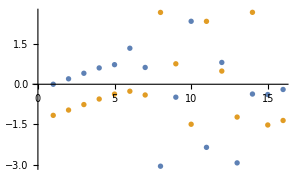
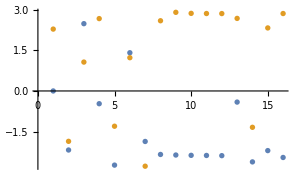
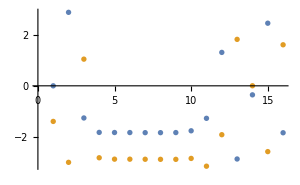
1 | 0.152047 | 148.391 | 0.428754 | 4.11074 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2 | 0.266561 | 148.391 | 0.748793 | 4.73668 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.304303 | 139.85 | 0.148423 | 14.8308 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.356361 | 266.2 | 1.44167 | 215.318 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 0.41793 | 148.478 | 1.20481 | 15.0372 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.416964 | 209.883 | 1.062 | 192.443 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.424398 | 150.328 | 1.06353 | 34.7125 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 0.430229 | 269.438 | 1.34564 | 170.887 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 0.430192 | 158.563 | 1.34546 | 178.372 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 0.434707 | 149.775 | 0.621141 | 13.55 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
11 | 0.431565 | 148.647 | 1.33094 | 32.0624 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
12 | 0.46314 | 148.406 | 0.333339 | 3.19406 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
13 | 0.468366 | 148.481 | 0.891609 | 10.9499 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
14 | 0.4674 | 150.844 | 0.852073 | 35.9069 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
15 | 0.471571 | 149.775 | 0.333064 | 11.0963 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
16 | 0.492869 | 148.391 | 0.160637 | 3.23531 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
17 | 0.509243 | 139.85 | 0.147634 | 14.8359 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
18 | 0.508282 | 148.497 | 0.586646 | 1.84005 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
19 | 0.507117 | 150.838 | 0.579878 | 16.6548 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
20 | 0.517306 | 148.647 | 1.01404 | 31.0495 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
21 | 0.534793 | 148.406 | 0.317131 | 2.4585 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
22 | 0.533317 | 150.578 | 0.315828 | 7.61169 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
23 | 0.548538 | 140.618 | 0.215185 | 3.61708 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
24 | 0.547103 | 141.782 | 0.21393 | 3.73234 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
25 | 0.593876 | 150.328 | 0.422203 | 13.6777 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
26 | 0.602607 | 148.65 | 0.692752 | 27.2662 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
27 | 0.678848 | 150.328 | 0.102657 | 11.0543 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
28 | 0.687692 | 148.697 | 0.373373 | 1.0305 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
29 | 0.680527 | 150.328 | 0.103373 | 11.1151 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
30 | 0.773655 | 150.328 | 0.051321 | 7.70574 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
phases2=Transpose[Catenate[{-Reverse[Transpose[phi]],-Reverse[Transpose[theta]]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
dphases2=(#-#[[1]]&/@phases2);
norms=Norm[Mod[#-dphases[[-1]]+Pi,2*Pi]-Pi]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
test=Norm[Mod[dphases[[-Round[period/0.1];;-1]]-dphases[[-10*Round[period/0.1];;-9*Round[period/0.1]-1]]+Pi,2*Pi]-Pi];
If[period>0,
{Grid[{{j,order,period,norm,test,rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

#### Plot auto results

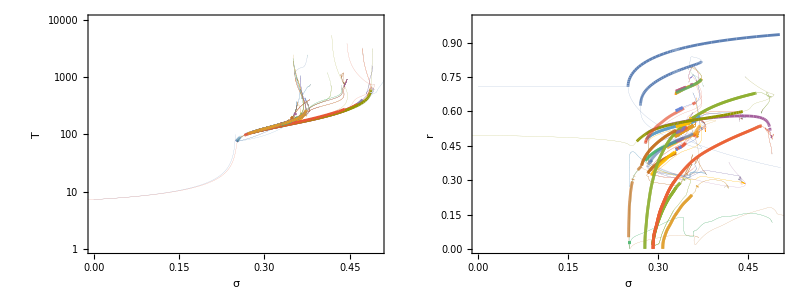

diagram.pdf

```mathematica
branches={DeleteCases[Import["auto/rel/steady.dat"],{}]};
stables={DeleteCases[DeleteCases[Import["auto/rel/steady.dat"],{}],u_/;u[[5]]<62]};
Monitor[Do[
If[FileExistsQ["auto/rel/"<>ToString[i]<>"fw.dat"]&&FileExistsQ["auto/rel/"<>ToString[i]<>"rv.dat"],
branch=Catenate[{Reverse[DeleteCases[Import["auto/rel/"<>ToString[i]<>"rv.dat"],{}]],DeleteCases[Import["auto/rel/"<>ToString[i]<>"fw.dat"],{}]}];AppendTo[branches,branch];
AppendTo[stables,DeleteCases[branch,u_/;u[[5]]<62]]];,{i,1,30}],i]
inds=First/@Position[Length/@branches,u_/;u>4];
sigmas=Range[0,0.25-0.001,0.001];
orders=Table[Mean[(1/(1+0.25*(1+4*sigma-((1-4*sigma)*(3+4*sigma))^0.5*Tan[(2*Pi/(0.75-2*sigma-4*sigma^2)^0.5*Range[0,100]/100*0.25*((1-4*sigma)*(3+4*sigma))^0.5)])^2))]^0.5,{sigma,sigmas}];
p=Grid[{{Show[ListLogPlot[Transpose[{sigmas,2*Pi/(0.75-2*sigmas-4*sigmas^2)^0.5}],PlotRange->{{0,0.5},{10^0,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1]]],Graphics[{Table[Table[If[branches[[j,i,5]]<62,{AbsoluteThickness[0.1],ColorData[97,"ColorList"][[1+Mod[j,15]]],Line[{{branches[[j,i,1]],Log[branches[[j,i,3]]]},{branches[[j,i+1,1]],Log[branches[[j,i+1,3]]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,2,Length[branches]}],Table[Table[If[branches[[j,i,5]]==62,{AbsoluteThickness[2],ColorData[97,"ColorList"][[1+Mod[j,15]]],Line[{{branches[[j,i,1]],Log[branches[[j,i,3]]]},{branches[[j,i+1,1]],Log[branches[[j,i+1,3]]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,2,Length[branches]}]}]],Show[ListPlot[Transpose[{sigmas,orders}],PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1]]],Graphics[{Table[Table[If[branches[[j,i,5]]<62,{AbsoluteThickness[0.1],ColorData[97,"ColorList"][[1+Mod[j-1,15]]],Line[{{branches[[j,i,1]],branches[[j,i,4]]},{branches[[j,i+1,1]],branches[[j,i+1,4]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,1,Length[branches]}],Table[Table[If[branches[[j,i,5]]==62,{AbsoluteThickness[2],ColorData[97,"ColorList"][[1+Mod[j-1,15]]],Line[{{branches[[j,i,1]],branches[[j,i,4]]},{branches[[j,i+1,1]],branches[[j,i+1,4]]}}]}],{i,1,Length[branches[[j]]]-1}],{j,1,Length[branches]}]}]]}}]
Export["diagram.pdf",p]
```

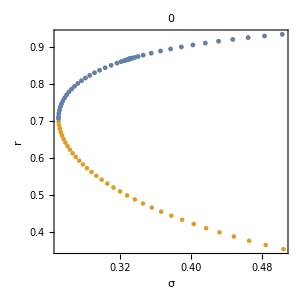
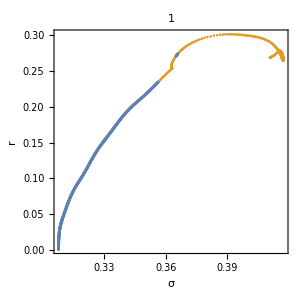
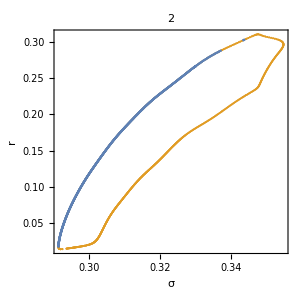
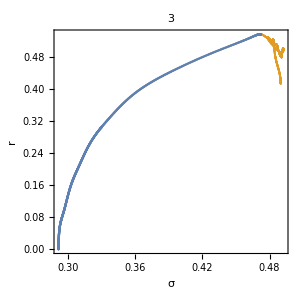
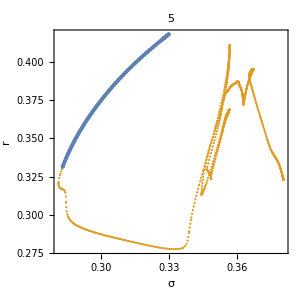
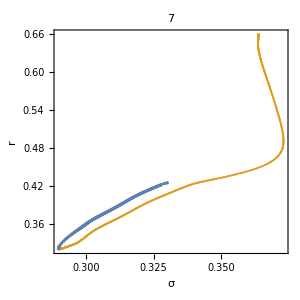
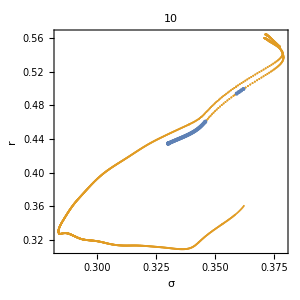
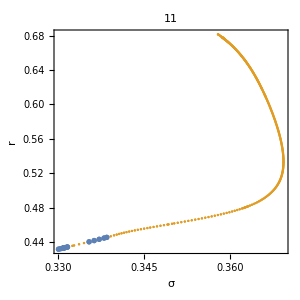

```mathematica
Show[ListPlot[branches[[#,All,{1,4}]],Joined->False,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[Dashed,ColorData[97,"ColorList"][[2]],AbsoluteThickness[1]]],ListPlot[stables[[#,All,{1,4}]],Joined->False,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2]]],PlotLabel->#-1,PlotRange->All]&/@inds
```

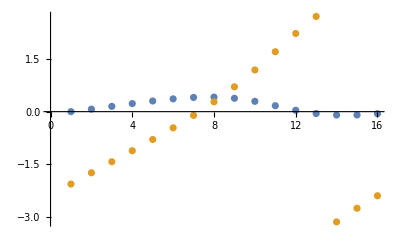

-Graphics- | -Graphics-

{1.,0.997411,0.98869,0.973753,0.954376,0.934271,0.919015,0.915374,0.928707,0.956959,0.98573,0.999195,0.998563,0.995329,0.995556,0.998297,0.,0.0719134,0.14997,0.227609,0.298606,0.356564,0.394223,0.402604,0.370815,0.290223,0.168331,0.0401252,-0.0535889,-0.0965373,-0.0941765,-0.058342,-0.470857,-0.16894,0.143964,0.442548,0.701979,0.895921,0.994299,0.961446,0.759718,0.373632,-0.135135,-0.609828,-0.908573,-0.999997,-0.924483,-0.733868,-0.88221,-0.985626,-0.989583,-0.896745,-0.712198,-0.444213,-0.106629,0.274995,0.650253,0.927577,0.990827,0.792534,0.417726,-0.00249988,-0.381222,-0.679292}

OutputStream[…]

OutputStream[…]

data/limitic.dat

```mathematica
dat=Partition[BinaryReadList["data/zerolimit.dat","Real64"],2501];
ind=1;
x=Catenate[{ConstantArray[1,{1,2501}],dat[[1;;15]]}];
y=Catenate[{ConstantArray[0,{1,2501}],dat[[16;;30]]}];
u=dat[[31;;46]];
v=dat[[47;;62]];
theta=ArcTan[x,y];
phi=ArcTan[u,v];
ListPlot[{theta[[All,ind]],phi[[All,ind]]}]

Grid[{{rasterizeBackground[ListDensityPlot[Transpose[theta],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[Transpose[phi],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]]}}]
ic=Catenate[{x[[All,1]],y[[All,1]],u[[All,1]],v[[All,1]]}]+0.0*RandomReal[{-1,1},64]
file=OpenWrite["data/limitic.dat",BinaryFormat->True]
BinaryWrite[file,ic,"Real64"]
Close[file]
```

```mathematica
DSolve[z'[t]==1+1/2*Sin[z[t]],z,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→Function[{t},-2 ArcTan[1/2 (1-√3 Tan[1/4 (√3 t+2 √3 C[1])])]]},{z→Function[{t},2 ArcTan[1/2 (-1+√3 Tan[1/4 (√3 t+2 √3 C[1])])]]}}

```mathematica
η[t_]:=-2 ArcTan[1/2 (1-√3 Tan[1/4 (√3 (t-Pi/(3/4)^(1/2)))])];
w1=0;
w2=0;
phases=Table[Flatten[{Cos[w1*#+η[2*Pi/(3/4)^(1/2)*m/1000]/2],Sin[w1*#+η[2*Pi/(3/4)^(1/2)*m/1000]/2],Cos[w2*#-η[2*Pi/(3/4)^(1/2)*m/1000]/2],Sin[w2*#-η[2*Pi/(3/4)^(1/2)*m/1000]/2]}&/@Range[M]],{m,1,1000}];
```

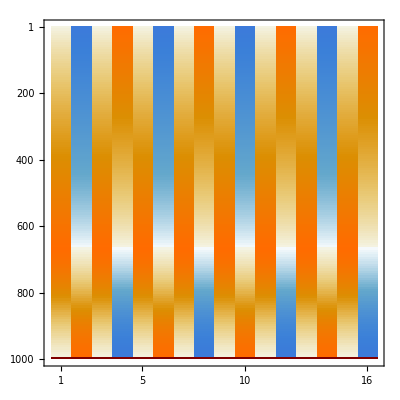

```mathematica
MatrixPlot[phases[[All,1;;16]],AspectRatio->1]
```

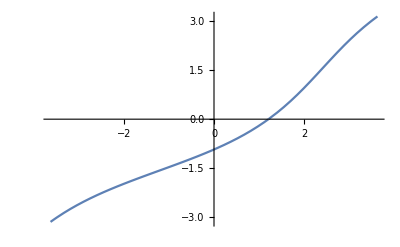

```mathematica
Plot[η[t],{t,-Pi/(3/4)^(1/2),Pi/(3/4)^(1/2)}]
```